```mathematica
eq=Binomial[1000,500]*(1+2f)^500*(1-f)^500==10^9
```

270288240945436569515614693625975275496152008446548287007392875106625428705522193898612483924502370165362606085021546104802209750050679917549894219699518475423665484263751733356162464079737887344364574161119497604571044985756287880514600994219426752366915856603136862602484428109296905863799821216320 (1-f)^500 (1+2 f)^500==1000000000

```mathematica
k=400;
g[k_]:=Module[{n=1000},
eq=Binomial[n,k]*(1+2f)^k*(1-f)^(n-k)==10^9;
eq2=MapAt[Simplify,Map[#/Binomial[n,k]&,eq],1];
(*Reduce[eq2,f,Reals]*)
(*NSolve[eq2,f]*)
Check[rel=FindRoot[eq2,{f,.9},WorkingPrecision->50],False]===False]
k=500;
While[g[k]==True&&k≤1000,
k++;]
{k,rel}
k=500;
While[g[k]==True&&k≥0,
k--;]
{k,rel}
```

{500,{f→0.90669465736549160554070532090876655936625073961394}}

{500,{f→0.90669465736549160554070532090876655936625073961394}}

```mathematica
eq2
Map[Refine[#^(1/500),#>0]&,eq2]
MapAt[Identity@@#&,%,1]
NSolve[%,f,WorkingPrecision->20]
```

(1+f-2 f^2)^500==3125000/844650752954489279736295917581172735925475026395463396898102734708204464704756855933164012264069906766758144015692331577506905468908374742343419436560995235698954638324224166738007700249180897951139294253498430014284515580488399626608128106935708601146612051884802695632763837841552830824374441301

Abs[1+f-2 f^2]==(2^(3/500) 5^(2/125))/(3^(1/125) 23^(1/250) 19712262898888872079542017726928813646187192849202161004879991008149652610440310297396999049314334214725154473049367116560640982727913714260389260812644291248312787657220102376671747304468736678828894355842573455956603784930532792518101428433235515441354805290317223170500217924375197340063349^(1/500))

1+f-2 f^2==(2^(3/500) 5^(2/125))/(3^(1/125) 23^(1/250) 19712262898888872079542017726928813646187192849202161004879991008149652610440310297396999049314334214725154473049367116560640982727913714260389260812644291248312787657220102376671747304468736678828894355842573455956603784930532792518101428433235515441354805290317223170500217924375197340063349^(1/500))

{{f→-0.40669465736549160554},{f→0.90669465736549160554}}

```mathematica
Binomial[1000,500]/2^1000
```

4223253764772446398681479587905863679627375131977316984490513673541022323523784279665820061320349533833790720078461657887534527344541873711717097182804976178494773191621120833690038501245904489755696471267492150071422577902441998133040640534678543005733060259424013478163819189207764154121872206505/167423219872854268898191413915625282900219501828989626163085998182867351738271269139562246689952477832436667643367679191435491450889424069312259024604665231311477621481628609147204290704099549091843034096141351171618467832303105743111961624157454108040174944963852221369694216119572256044331338563584

```mathematica
{85,{f->0.2836139488408744410738371752443230857595832591388272781317281136904`50.}}
{123,{f->0.3793506899884366253272803845681602113409518021959592266557854335339`50.}}
{164,{f->0.4700448447241219174265198727218871986533951666073967117731400245639`50.}}
{212,{f->0.5629802152978194204957846904725738053970875354666237209955015673507`50.}}
{266,{f->0.6531691211260309094033159285153738810273084793804042959297949038398`50.}}
{500,{f->0.9066946573654916055407053209087665593662507396139411578702853978215`50.}}
```

```mathematica
Simplify[(1+2f)^500*(1-f)^500==10^9]
```

(1+f-2 f^2)^500==1000000000

```mathematica
NSolve[1+f-2 f^2==1000000000^(1/500),f,WorkingPrecision->12]
```

{{f→0.0466744351948},{f→0.453325564805}}

```mathematica
(1+2f)^500*(1-f)^500/.f->.453325564805
```

1.×10^9

```mathematica
Map[Binomial[20,#]&,Range[20]]
```

{20,190,1140,4845,15504,38760,77520,125970,167960,184756,167960,125970,77520,38760,15504,4845,1140,190,20,1}

```mathematica
Solve[(1+2f)(1-f)==1]
```

{{f→0},{f→1/2}}

```mathematica
Clear["Global`*"]
```

```mathematica
hh[f_]:=Position[(g[f,#]>10^9)&/@Range[0,1000],True]
```

```mathematica
hh[.6]
hh[.25]
```

```mathematica
g[.15,432]
```

1.35981×10^9

```mathematica
n=1000;
g[f_,k_]:=(1+2f)^k*(1-f)^(n-k);
h[f_]:=Min@@Position[(g[f,#]>10^9)&/@Range[0,1000],True]
(*Ordering[h/@Range[0.0001,1,0.001]]*)
```

```mathematica
h[.2]
```

437

```mathematica
h[.09]
```

444

```mathematica
h[.15]
```

433

```mathematica
N[Sum[Binomial[n,i],{i,432,1000}]/2^n,12]
```

0.999992836187

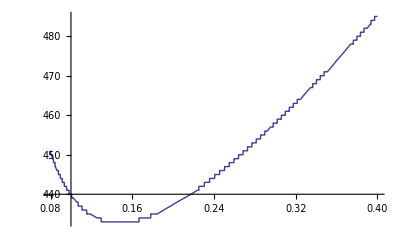

```mathematica
Plot[h[f],{f,.08,.4}]
```

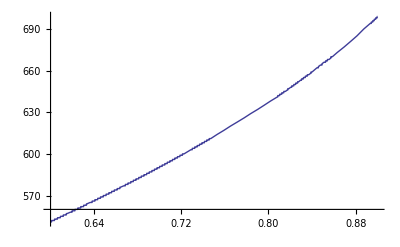

```mathematica
Plot[h[f],{f,.6,.9}]
```